# Tips & Tricks: Mathematica for Research

## Q&A (04/05/2026)

```mathematica
Quit[]
```

### Delayed Rule/Replace

```mathematica
c=15
rule1={exp->1+c} (* -> evaluates the RHS immediately and that's how the rule is defined *)
rule2={exp_:>1+c}(* :> uses delayed evaluation; it only defines the rule when you use it *)
```

15

{exp→16}

{exp_:>1+c}

```mathematica
exp/.rule1
exp/.rule2
c=-15;
exp/.rule1 (* Note that rule1 did not change when we change the value of c *)
exp/.rule2 (* In contrast, rule2 changes when we change the value of c *)
```

16

16

16

-14

```mathematica
(* Note similarity with Delayed Evaluation *)
```

```mathematica
c=15
f[a_]=1+c
g[a_]:=1+c
{f[1],g[1]}
```

15

16

{16,16}

```mathematica
c=-15
{f[1],g[1]} (* f[1] uses original value of c, because f was defined with "immediate evaluation"; g[1] uses updated value of c, because g was defined with "delayed evaluation", so it always waits for the most up to date values of everything *)
```

-15

{16,-14}

### Replace vs ReplaceAll

```mathematica
?ReplaceAll
?Replace
```

```mathematica
exp^3/.{exp^(n_.):>exp^(n-1)} (* /. = Replace; it only applies the rules once *)
exp^3//.{exp^(n_.):>exp^(n-1)} (* //. = ReplaceAll; it keeps applying rules until there is no match, including to expressions that are a result of previous replacements *)
```

exp^2

1

```mathematica
(* You might want to use ReplaceAll e.g. when some rules transform your expression into something that matches a different rule *)
a+b^2/.{b^n_:>b^(n-1),a+b:>1}
a+b^2//.{b^n_:>b^(n-1),a+b:>1}
```

a+b

1

### Defaults & Patterns

```mathematica
exp^3//.{exp^n_:>exp^(n-1)} (* exp^n_ looks for Power[exp,n] *)
FullForm/@{exp^3,exp} (* But exp is not Power[exp,1] for Mathematica, even though we know it's the same *)
exp^3//.{exp^(n_.):>exp^(n-1)} (* exp^(n_.) with the . in front of n_ looks for Power[exp,n] and if it doesn't find the n_ uses the Power[_,_] default value, which is 1 *)
```

exp

{Power[exp,3],exp}

1

```mathematica
(* You can check a function's default with ??function *)
??Power
```

#### Replace with Levelspec

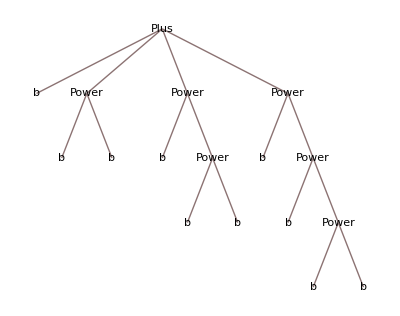

b+3 a

b+3 a

b+b^b+2 b^a

b+b^b+b^(b^b)+b^(b^(b^b))

b+b^(b^a)+b^a+a

```mathematica
b+b^b+b^(b^b)+b^(b^(b^b))//TreeForm
b+b^b+b^(b^b)+b^(b^(b^b))/.{b^n_:>Style[a,Red]}(* Most common replace, no specification; find the pattern in 3 different terms *)
Replace[b+b^b+b^(b^b)+b^(b^(b^b)),{b^n_:>Style[a,Red]},{1}](* Match pattern specifically at level 1 *)
Replace[b+b^b+b^(b^b)+b^(b^(b^b)),{b^n_:>Style[a,Red]},{2}](* Match pattern specifically at level 2 ; it does not touch the b^n at level 1 *)
Replace[b+b^b+b^(b^b)+b^(b^(b^b)),{b^n_:>Style[a,Red]},{-1}](* Match pattern specifically at highest/last level ; it does not find a Power[b,_] *)
Replace[b+b^b+b^(b^b)+b^(b^(b^b)),{b^n_:>Style[a,Red]},{-2}](* Match pattern specifically at 2nd highest level ; it finds and replaces only at this level *)
```

```mathematica
(a+a x +b x+x^2)/.{a x:>1/n x}
```

a+b x+x/n+x^2

### Simplify & Assumptions

```mathematica
√(1/x)x^(1/2)//Simplify (* For general x, Mathematica does not simplify this expression; it does not know if its allowed *)
```

√(1/x) √x

```mathematica
$Assumptions={x>=0} (* We can add the assumption that non-negative, and now it does Simplify the expression *)
√(1/x)x^(1/2)//Simplify
```

{x≥0}

1

```mathematica
√(1/y)y^(1/2)//Simplify
√(1/y)y^(1/2)//Simplify[#,{y>=0}]&(* We can also add the assumption locally in Simplify, rather than globally *)
```

√(1/y) √y

1

```mathematica
Log[a]-Log[b]//Simplify[#,{a>0,b>0}]&
```

Log[x/y]

```mathematica
Exp[(Log[a]-Log[b])/q]//FullSimplify (*Mathematica is not sure whether it's okay to simplify, so it does nothing*)
Exp[(Log[a]-Log[b])/q]//FullSimplify[#,{a>=0,b>=0}]& (*Assuming a,b ≥ 0 it know it's okay and it simplifies*)
```

ⅇ^((Log[a]-Log[b])/q)

(a/b)^(1/q)

```mathematica
Exp[Log[a]/q-Log[b]/q]//FullSimplify (*This seems equivalent, but internally its different*)
```

a^(1/q) b^(-1/q)

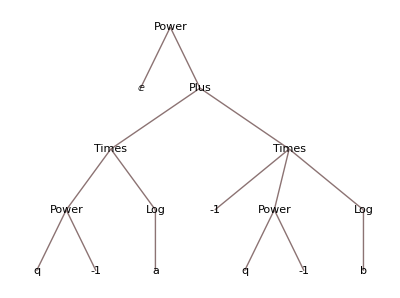
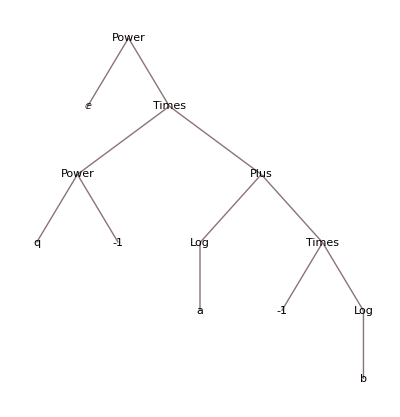

```mathematica
TreeForm/@{Exp[Log[a]/q-Log[b]/q],Exp[(Log[a]-Log[b])/q]} (* Exp[Plus[_]] vs Exp[Times[_]] *)
```

```mathematica
Exp[(Log[a]-Log[b])/q]/.{Exp[a_]:>Exp[a//Expand]}//FullSimplify (* Since now we know Mathematica deals with Exp[Plus[_]] better, we might want to expand all the exponents before using FullSimplify *)
```

a^(1/q) b^(-1/q)

#### Complex | Re[] & Im[]

```mathematica
sol=z/.Solve[1+α z+β z^3==0,z]
```

{-((2/3)^(1/3) α)/((-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))+((-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))/(2^(1/3) 3^(2/3) β),((1+ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))-((1-ⅈ √3) (-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))/(2 2^(1/3) 3^(2/3) β),((1-ⅈ √3) α)/(2^(2/3) 3^(1/3) (-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))-((1+ⅈ √3) (-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))/(2 2^(1/3) 3^(2/3) β)}

```mathematica
sol[[1]]//Re (* Since Mathematica does not know whether α,β are Real AND whether (...)^(1/3) comes out Real, Re[_] does nothing *)
```

Re[-((2/3)^(1/3) α)/((-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))+((-9 β^2+√3 √(4 α^3 β^3+27 β^4))^(1/3))/(2^(1/3) 3^(2/3) β)]

```mathematica
?ComplexExpand
sol[[1]]//ComplexExpand (*ComplexExpand assumes that every variable is Real and expands the result; this can be messy... *)
```

-((2/3)^(1/3) α Cos[1/3 Arg[-9 β^2+√3 √(4 α^3 β^3+27 β^4)]])/(((-9 β^2+√3 ((4 α^3 β^3+27 β^4)^2)^(1/4) Cos[1/2 Arg[4 α^3 β^3+27 β^4]])^2+3 √((4 α^3 β^3+27 β^4)^2) Sin[1/2 Arg[4 α^3 β^3+27 β^4]]^2)^(1/6))+1/(2^(1/3) 3^(2/3) β)Cos[1/3 Arg[-9 β^2+√3 √(4 α^3 β^3+27 β^4)]] ((-9 β^2+√3 ((4 α^3 β^3+27 β^4)^2)^(1/4) Cos[1/2 Arg[4 α^3 β^3+27 β^4]])^2+3 √((4 α^3 β^3+27 β^4)^2) Sin[1/2 Arg[4 α^3 β^3+27 β^4]]^2)^(1/6)+ⅈ (((2/3)^(1/3) α Sin[1/3 Arg[-9 β^2+√3 √(4 α^3 β^3+27 β^4)]])/(((-9 β^2+√3 ((4 α^3 β^3+27 β^4)^2)^(1/4) Cos[1/2 Arg[4 α^3 β^3+27 β^4]])^2+3 √((4 α^3 β^3+27 β^4)^2) Sin[1/2 Arg[4 α^3 β^3+27 β^4]]^2)^(1/6))+1/(2^(1/3) 3^(2/3) β)((-9 β^2+√3 ((4 α^3 β^3+27 β^4)^2)^(1/4) Cos[1/2 Arg[4 α^3 β^3+27 β^4]])^2+3 √((4 α^3 β^3+27 β^4)^2) Sin[1/2 Arg[4 α^3 β^3+27 β^4]]^2)^(1/6) Sin[1/3 Arg[-9 β^2+√3 √(4 α^3 β^3+27 β^4)]])

```mathematica
sol[[1]]//ComplexExpand //Simplify[#,{α>=0,β>=0}]&
```

(-2 α+2^(2/3) (2 α^3+27 β-3 √3 √(β (4 α^3+27 β)))^(1/3))/(2^(5/6) √3 (β^3 (2 α^3+27 β-3 √3 √(β (4 α^3+27 β))))^(1/6))

### CoefficientList, CoefficientArray, CoefficientRule

```mathematica
poly=(1+5x)(2x+3 y^3)^2//Expand
```

4 x^2+20 x^3+12 x y^3+60 x^2 y^3+9 y^6+45 x y^6

```mathematica
?CoefficientRules
CoefficientRules[poly,{x,y}] (* Returns list of rules, a·x^n y^m gives {n,m}->a *)
%/.{Rule[{m_,n_},a_]:>Rule[x^m y^n,a]} (* We could transform it in different ways, as needed *)
%%/.{Rule[{m_,n_},a_]:>{x^m y^n,a}}//TableForm
```

{{3,0}→20,{2,3}→60,{2,0}→4,{1,6}→45,{1,3}→12,{0,6}→9}

{x^3→20,x^2 y^3→60,x^2→4,x y^6→45,x y^3→12,y^6→9}

x^3 | 20
x^2 y^3 | 60
x^2 | 4
x y^6 | 45
x y^3 | 12
y^6 | 9

```mathematica
(1+5x)(2x+3 y^3)^2(x+y+z^2)//Expand
CoefficientRules[%,{x,y,z}]/.{Rule[{m_,n_,p_},a_]:>{x^m y^n z^p,a}}//TableForm
```

4 x^3+20 x^4+4 x^2 y+20 x^3 y+12 x^2 y^3+60 x^3 y^3+12 x y^4+60 x^2 y^4+9 x y^6+45 x^2 y^6+9 y^7+45 x y^7+4 x^2 z^2+20 x^3 z^2+12 x y^3 z^2+60 x^2 y^3 z^2+9 y^6 z^2+45 x y^6 z^2

x^4 | 20
x^3 y^3 | 60
x^3 y | 20
x^3 z^2 | 20
x^3 | 4
x^2 y^6 | 45
x^2 y^4 | 60
x^2 y^3 z^2 | 60
x^2 y^3 | 12
x^2 y | 4
x^2 z^2 | 4
x y^7 | 45
x y^6 z^2 | 45
x y^6 | 9
x y^4 | 12
x y^3 z^2 | 12
y^7 | 9
y^6 z^2 | 9

```mathematica
(* In some cases we could also try defining similar "selection functions" using Replacements *)
(1+x)(2x+y^3)^2//Expand
List@@%
Replace[%,{num_.var_:>{var,num}/;NumericQ[num]},1]
```

4 x^2+4 x^3+4 x y^3+4 x^2 y^3+y^6+x y^6

{4 x^2,4 x^3,4 x y^3,4 x^2 y^3,y^6,x y^6}

{{x^2,4},{x^3,4},{x y^3,4},{x^2 y^3,4},{y^6,1},{x y^6,1}}

### NIntegrate

```mathematica
?Circle
```

```mathematica
NIntegrate[x^3 y^2+1,{x,y}∈Circle[{0,0},1]]
NIntegrate[x^3 y^2+1,{x,y}∈Circle[{0,0},1],Method->"MultidimensionalRule"](*Some Methods cannot be used in certain cases*)
NIntegrate[x^3 y^2+1/.{x->r Cos[θ],y->r Sin[θ]},{r,0,1},{θ,0,2π},Method->"MultidimensionalRule"]
```

6.28319

NIntegrate::regm: Method MultiDimensionalRule is not applicable for a region domain. Continuing with method Automatic.

6.28319

6.28319

```mathematica
(* Sometimes it's better to restructure the Input rather that deal with Mathematica's options; e.g. with NIntegrate, it's easy to impose symmetries/deal with cancelations, because we cannot explicitly choose a symmetric grid *)
```

```mathematica
f[x_]:=100(1/(√(2π)σ)Exp[-(x-μ)^2/(2 σ^2)]-1/(√(2π)σ)Exp[-(x+μ)^2/(2 σ^2)])/.{μ->1,σ->1/10}
```

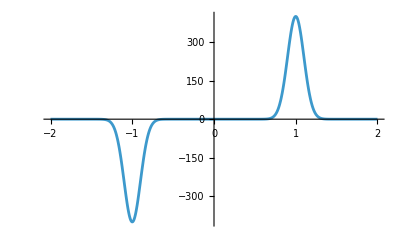

```mathematica
Plot[f[x],{x,-2,2},PlotRange->All]
```

```mathematica
NIntegrate[f[x],{x,-2,2}](*You get some error, due to cancellations on the Left and Right*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.039}. NIntegrate obtained -1.77636×10^-15 and 2.98428×10^-14 for the integral and error estimates.

-1.77636×10^-15

```mathematica
Integrate[f[x],{x,-2,2}]
```

0

### Kernels

Different notebooks running on the same Kernel are just different windows to the same thing. 
If Notebook1.nb and Notebook2.nb are using the same Kernel, definition you make in Notebook1.nb exist also in Notebook2.nb.

E.g: 
Notebook1.nb   c=1; 
Notebook2.nb   c 
                                 1

If you want them to be independent, change the Kernel of Notebook2.nb, 
Evaluation > Notebook’s Kernel > “other Kernel”

E.g: 
Notebook1.nb   c=1; 
Notebook2.nb   c 
                                 c